# 一些有趣的极限

```mathematica
Sum[1/x^n,{n,1,Infinity}]
```

1/(-1+x)

```mathematica
Manipulate[Sum[1/x^n,{n,1,Infinity}],{{x,6},1,10}]
```

```mathematica
1/5.5
```

0.181818

### 下面两个在取整数时相等

```mathematica
Manipulate[{Sum[x^2,{x,1,n}],1/6 n(n+1)(2n+1)},{{n,5},1,100}]
```

```mathematica
Manipulate[{Sum[x^3,{x,1,n}],((n(n+1))/2)^2},{{n,5},1,100}]
```

```mathematica
Limit[x/Sin[x],x->0]
```

1

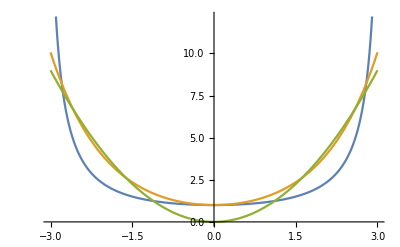

```mathematica
Plot[{x/Sin[x],Cosh[x],x^2},{x,-3,3}]
```

```mathematica
Limit[x/Log[x+1],x->0]
```

1

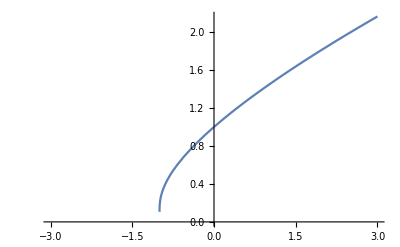

```mathematica
Plot[x/Log[x+1],{x,-3,3}]
```